```mathematica
(* 01 *)
data29 = Table[Prime[i]^i,{i,1,10}]
```

{2,9,125,2401,161051,4826809,410338673,16983563041,1801152661463,420707233300201}

```mathematica
(* 02 *)
data29[[3]]
```

125

```mathematica
(* 03 *)
Table[data29[[i]],{i,{1,3,4}}]
```

{2,125,2401}

```mathematica
Total[{2,125,2401}]
```

2528

```mathematica
(* 04 *)
data29[[2;;6]]
```

{9,125,2401,161051,4826809}

```mathematica
(* 05 *)
data29 = Table[
{i,i^i,i-i^i},
{i,1,4}
]
```

{{1,1,0},{2,4,-2},{3,27,-24},{4,256,-252}}

```mathematica
(* 06 *)
data29[[2]]
```

{2,4,-2}

```mathematica
(* 07 *)
data29[[2,3]]
```

-2

```mathematica
(* 08 *)
data33 = Table[
	data29[[i,2]],
	{i,1,Length[data29]}
]
```

{1,4,27,256}

```mathematica
(* 09 *)
data33[[4]] = data33[[4]]^2
```

65536

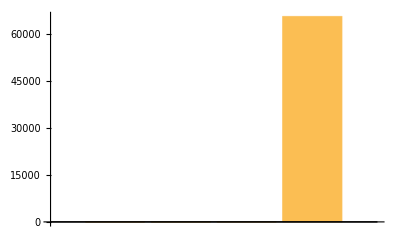

```mathematica
(* 10 *)
BarChart[data33]
```